```mathematica
c=Array[0,{4,16,16}];
cdag=Array[0,{4,16,16}];
Table[c[[i+1,;;,;;]]=ArrayReshape[ReadList["~/Libraries/NEdyson/ED/hybfermion/build/c_"<>ToString[i]<>".dat",Number],{16,16}],{i,0,3}];
Table[cdag[[i+1,;;,;;]]=ArrayReshape[ReadList["~/Libraries/NEdyson/ED/hybfermion/build/cdag_"<>ToString[i]<>".dat",Number],{16,16}],{i,0,3}];
IM=IdentityMatrix[16];
```

```mathematica
t=1;U=1;μ=0;ϵ0=0;ϵ1=0;β=20;
H=-t(cdag[[1]].c[[3]]+cdag[[3]].c[[1]]+cdag[[2]].c[[4]]+cdag[[4]].c[[2]]) +U((cdag[[1]].c[[1]]-1/2 IM).(cdag[[2]].c[[2]]-1/2 IM)+(cdag[[3]].c[[3]]-1/2 IM).(cdag[[4]].c[[4]]-1/2 IM))-μ(cdag[[1]].c[[1]]+cdag[[2]].c[[2]]+cdag[[3]].c[[3]]+cdag[[4]].c[[4]])+ϵ0 cdag[[1]].c[[1]]+ϵ0 cdag[[2]].c[[2]]+ϵ1 cdag[[3]].c[[3]]+ϵ1 cdag[[4]].c[[4]];
Z=N[Tr[MatrixExp[-β H]]];
HEigVals =N[ Eigenvalues[H]]
HEigVecs = Map[Normalize,Eigenvectors[H]];
N[HEigVecs.Transpose[HEigVecs]]
cdagTrans=Table[HEigVecs.cdag[[i]].Transpose[HEigVecs],{i,1,4}];
cTrans=Table[HEigVecs.c[[i]].Transpose[HEigVecs],{i,1,4}];
```

{-2.06155,2.06155,-1.,-1.,-1.,-1.,1.,1.,1.,1.,-0.5,-0.5,-0.5,0.5,0.5,0.5}

{{1.,2.77556×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{2.77556×10^-17,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}}

## Free Matsubara

```mathematica
ReadFile=OpenRead["~/Libraries/NEdyson/build/programs/Gfree_GM.dat"];
Table[Read[ReadFile,Number],{i,1,6}];
GMFreeMyCode=Table[Table[Read[ReadFile,Number],{t,1,8}],{t,1,601}];
```

```mathematica
GM=-Table[Table[Table[1/Z Tr[MatrixExp[(-β+τ)H].c[[i]].MatrixExp[-τ H].cdag[[j]]],{τ,0,β,β/100}],{i,1,4}],{j,1,4}];
```

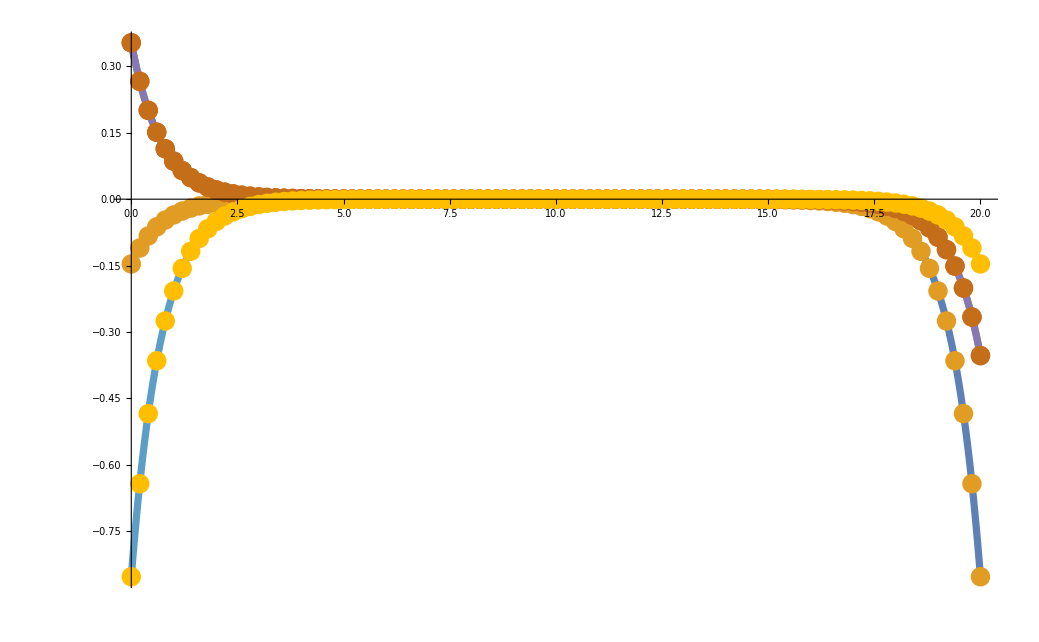

```mathematica
ListPlot[{Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,1]]}],Transpose[{Range[0,β,β/100],GM[[1,1,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,3]]}],Transpose[{Range[0,β,β/100],GM[[1,3,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,5]]}],Transpose[{Range[0,β,β/100],GM[[3,1,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,7]]}],Transpose[{Range[0,β,β/100],GM[[3,3,;;]]}]},PlotRange->Full,Joined->{True, False,True, False,True, False,True, False},PlotStyle->{Thickness[0.005]},PlotMarkers->{None,Style[•,20],None,Style[•,20],None,Style[•,20],None,Style[•,20]}]
```

```mathematica
GMInteract=-Table[Table[Table[1/Z Tr[MatrixExp[(-β+τ)H].c[[i]].MatrixExp[-τ H].cdag[[j]]],{τ,0,β,β/100}],{i,1,4}],{j,1,4}];
```

$Aborted

```mathematica
ReadFile=OpenRead["~/Libraries/NEdysondata/noquench/N2U1B20/Ntau600Nt1600/G_GM.dat"];
Table[Read[ReadFile,Number],{i,1,6}];
GMFreeMyCode=Table[Table[Read[ReadFile,Number],{t,1,8}],{t,1,601}];
```

```mathematica
ReadFile=OpenRead["~/Libraries/NEdyson/build/programs/Gfree_GM.dat"];
Table[Read[ReadFile,Number],{i,1,6}];
GMFreeMyCode=Table[Table[Read[ReadFile,Number],{t,1,8}],{t,1,601}];
```

## Retarded

```mathematica
GRInt=-Table[Table[Table[1/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β-I t)HEigVals]].HEigVecs.c[[i]].Transpose[HEigVecs].DiagonalMatrix[Exp[(-I t)HEigVals]].HEigVecs.cdag[[j]]],{t,0,24,24/1000}],{i,1,4,2}],{j,1,4,2}];
```

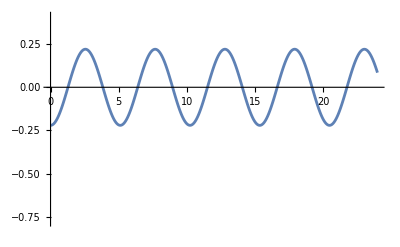

```mathematica
ListPlot[{Transpose[{Range[0,24,24/1000],Re[GRInt[[1,1,;;]]]}],Transpose[{Range[0,24,24/1000],GRInt[[1,2,;;]]}],Transpose[{Range[0,24,24/1000],GRInt[[2,1,;;]]}],Transpose[{Range[0,24,24/1000],GRInt[[2,2,;;]]}]},PlotRange->Full,Joined->{True,True,True,True},PlotStyle->{Thickness[0.005]},PlotMarkers->{None,None,None,None}]
```

```mathematica
GL=Table[Table[Table[I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β+I t)HEigVals]].HEigVecs.cdag[[j]].Transpose[HEigVecs].DiagonalMatrix[Exp[(I t)HEigVals]].HEigVecs.c[[i]]],{t,0,24,24/200}],{i,1,4,2}],{j,1,4,2}];
GG = Table[Table[Table[-I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β-I t)HEigVals]].HEigVecs.c[[i]].Transpose[HEigVecs].DiagonalMatrix[Exp[-I t HEigVals]].HEigVecs.cdag[[j]]],{t,0,24,24/200}],{i,1,4,2}],{j,1,4,2}];
GR = GG-GL;
```

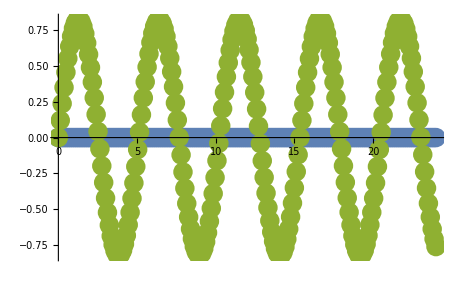

```mathematica
ListPlot[{Transpose[{Range[0,24,24/200],Im[GR[[2,1,;;]]]}],Transpose[{Range[0,24+1/1600,24/1600],GRMyCode[[;;,6]]}],Transpose[{Range[0,24,24/200],Re[GR[[2,1,;;]]]}],Transpose[{Range[0,24+1/1600,24/1600],GRMyCode[[;;,5]]}]},PlotRange->Full,Joined->{False,True},PlotStyle->{Thickness[0.005]},PlotMarkers->{Style[•,20],None}]
```

```mathematica
ReadFile=OpenRead["~/Libraries/NEdyson/python/plot/GRdata"];
GRMyCode=Table[Table[Read[ReadFile,Number],{i,1,8}],{t,1,1601}];
```

```mathematica
Length[GMFreeMyCode]
```

1601

```mathematica
GLf[t_,tp_,i_,j_]:=I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β+I t-I tp)HEigVals]].HEigVecs.cdag[[j]].Transpose[HEigVecs].DiagonalMatrix[Exp[(I t-I tp)HEigVals]].HEigVecs.c[[i]]];
GGf[t_,tp_,i_,j_]:=-I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β-I t+I tp)HEigVals]].HEigVecs.c[[i]].Transpose[HEigVecs].DiagonalMatrix[Exp[(-I t +I tp)HEigVals]].HEigVecs.cdag[[j]]];
GRf[t_,tp_,i_,j_]:= GGf[t,tp,i,j]-GLf[t,tp,i,j];
```

```mathematica
FTf[tav_,w_,i_,j_]:=-1/Pi Im[NIntegrate[GRf[tav+trel/2,tav-trel/2,i,j]Exp[I w trel],{trel,0,tav*2}]];
```

```mathematica
FTfTable=Table[FTf[24,w,1,1],{w,-3,3,0.01}];
```

$Aborted

```mathematica
FTfTable12=Table[FTf[24,w,1,3],{w,-3,3,0.01}];
```

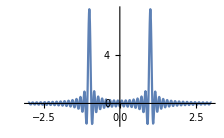

```mathematica
wlist=Table[w,{w,-3,3,0.01}];
plotlist = Transpose[{wlist,FTfTable[[;;]]}];
ListPlot[plotlist,Joined->True,PlotRange->Full]
```

```mathematica
a6=OpenWrite["calc8.dat",FormatType->OutputForm];
Table[Write[a6,ToString[DecimalForm[FTfTable[[w]],{∞,9}]]],{w,1,201}];
Close[a6];
```

```mathematica
GLf1D[t_,i_,j_]:=I/Z Tr[DiagonalMatrix[Exp[-(β+I t)HEigVals]].cdagTrans[[j]].DiagonalMatrix[Exp[(I t)HEigVals]].cTrans[[i]]];
GGf1D[t_,i_,j_]:=-I/Z Tr[DiagonalMatrix[Exp[-(β-I t)HEigVals]].cTrans[[i]].DiagonalMatrix[Exp[(-I t )HEigVals]].cdagTrans[[j]]];
GRf1D[t_,i_,j_]:= GGf1D[t,i,j]-GLf1D[t,i,j];FTf1D[tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1D[trel,i,j]Exp[I w trel],{trel,0,tmax}]];
```

```mathematica
FTf1DTable11=Table[FTf1D[100,w,1,1],{w,-4,4,0.01}];
```

{-0.0647101,-0.0171482,0.0464939,0.0677106,0.0267064,-0.0391422,-0.0693538,-0.0358896,0.0308306,0.0695779,0.0445,-0.0217113,-0.068349,-0.0523475,0.0119562,0.0656618,0.0592531,-0.00175414,-0.0615407,-0.0650532,-0.00869301,0.0560397,0.0696026,0.0191736,-0.0492421,-0.0727787,-0.0294704,0.0412595,0.0744832,0.0393646,-0.0322302,-0.0746455,-0.0486402,0.0223171,0.0732243,0.0570882,-0.011705,-0.0702092,-0.0645108,0.000597611,0.0656211,0.0707252,0.0107859,-0.059513,-0.0755676,-0.0222147,0.0519693,0.0788963,0.0334504,-0.0431048,-0.0805947,-0.0442512,0.033063,0.0805737,0.054376,-0.0220138,-0.0787728,-0.0635882,0.0101504,0.0751607,0.0716593,0.00231393,-0.069735,-0.0783717,-0.0151505,0.0625191,0.0835202,0.02812,-0.053557,-0.0869106,-0.040978,0.0429037,0.088354,0.0534828,-0.0306059,-0.0876526,-0.0654048,0.016664,0.084563,0.0765421,-0.000947546,-0.078706,-0.0867527,-0.0170277,0.0693067,0.0960406,0.0388238,-0.0542452,-0.104892,-0.0704838,0.0246623,0.116712,0.159092,0.155388,0.141532,0.140226,0.135797,0.0949975,0.0115867,-0.073188,-0.0998761,-0.0459521,0.0460536,0.0987607,0.0658378,-0.0251871,-0.0945414,-0.0800618,0.00637841,0.0878667,0.0907302,0.0114271,-0.0790305,-0.098516,-0.0284689,0.0682525,0.103652,0.0446964,-0.0557486,-0.106217,-0.0599375,0.0417529,0.10624,0.0739661,-0.0265244,-0.103746,-0.0865358,0.010348,0.0987806,0.0973994,0.00646785,-0.091418,-0.106322,-0.0235948,0.0817705,0.113089,0.0406896,-0.0699905,-0.117516,-0.0573994,0.0562713,0.119456,0.0733681,-0.0408466,-0.1188,-0.0882427,0.0239886,0.115484,0.10168,-0.0060045,-0.109494,-0.113353,-0.012767,0.100866,0.122957,0.0319611,-0.0896874,-0.130219,-0.0511922,0.0760977,0.1349,0.0700603,-0.0602885,-0.136802,-0.0881575,0.0425016,0.135774,0.105076,-0.0230262,-0.131716,-0.120412,0.00219597,0.124581,0.133781,0.0196158,-0.114383,-0.144814,-0.0420009,0.10119,0.153176,0.0645222,-0.0851353,-0.158565,-0.0867205,0.0664101,0.160723,0.108121,-0.0452659,-0.159439,-0.128242,0.0220119,0.154559,0.1466,0.00298834,-0.145987,-0.162723,-0.0293199,0.133688,0.176152,0.0565219,-0.117697,-0.186455,-0.0840925,0.0981142,0.19323,0.111495,-0.0751112,-0.196116,-0.138166,0.0489287,0.194798,0.16352,-0.0198763,-0.189013,-0.186958,-0.0116687,0.178558,0.207876,0.0452648,-0.16329,-0.225673,-0.0804089,0.143136,0.239753,0.116541,-0.118089,-0.249537,-0.153047,0.0882117,0.254468,0.189266,-0.0536394,-0.254011,-0.224493,0.0145744,0.24766,0.257984,0.028715,-0.234934,-0.288958,-0.0758987,0.21538,0.316597,0.126591,-0.188557,-0.34005,-0.180359,0.154033,0.358418,0.236731,-0.111356,-0.370749,-0.295211,0.0600241,0.376009,0.355293,0.000564095,-0.373047,-0.416482,-0.0711892,0.360525,0.478321,0.152934,-0.336808,-0.54043,-0.247384,0.29978,0.602563,0.356965,-0.246514,-0.664706,-0.485549,0.172665,0.727243,0.639599,-0.0712904,-0.791282,-0.830539,-0.0696973,0.859369,1.08018,0.273627,-0.937263,-1.43519,-0.592331,1.03931,2.01461,1.1688,-1.21035,-3.23412,-2.59313,1.6861,8.21819,13.8436,15.5402,12.3702,6.09253,0.00621583,-3.14801,-2.76349,-0.397013,1.61528,1.84088,0.524414,-0.960836,-1.38146,-0.578756,0.587034,1.08996,0.599831,-0.340525,-0.878176,-0.601335,0.16428,0.710854,0.58943,-0.0323244,-0.571406,-0.56747,-0.0688301,0.451187,0.537585,0.146884,-0.345394,-0.501324,-0.206583,0.251255,0.459934,0.251055,-0.167137,-0.4145,-0.282501,0.0920741,0.366018,0.302574,-0.025496,-0.315428,-0.3126,-0.0329356,0.263626,0.313711,0.083429,-0.211479,-0.306919,-0.126131,0.159817,0.293175,0.16117,-0.109432,-0.273394,-0.188692,0.061071,0.248472,0.208875,-0.015431,-0.219299,-0.22195,-0.0268513,0.186759,0.228205,0.0652057,-0.151729,-0.227995,-0.0991356,0.115079,0.221738,0.128225,-0.0776585,-0.209919,-0.152143,0.0402956,0.193086,0.17065,-0.00378523,-0.171841,-0.183597,-0.0311186,0.146839,0.190935,0.0637122,-0.118776,-0.192704,-0.0933508,0.0883844,0.189046,0.119457,-0.0564164,-0.180189,-0.141527,0.0236391,0.166454,0.159141,0.00917865,-0.148245,-0.171965,-0.0412776,0.126041,0.179757,0.0719188,-0.100395,-0.182371,-0.100395,0.0719188,0.179757,0.126041,-0.0412776,-0.171965,-0.148245,0.00917865,0.159141,0.166454,0.0236391,-0.141527,-0.180189,-0.0564164,0.119457,0.189046,0.0883844,-0.0933508,-0.192704,-0.118776,0.0637122,0.190935,0.146839,-0.0311186,-0.183597,-0.171841,-0.00378523,0.17065,0.193086,0.0402956,-0.152143,-0.209919,-0.0776585,0.128225,0.221738,0.115079,-0.0991356,-0.227995,-0.151729,0.0652057,0.228205,0.186759,-0.0268513,-0.22195,-0.219299,-0.015431,0.208875,0.248472,0.061071,-0.188692,-0.273394,-0.109432,0.16117,0.293175,0.159817,-0.126131,-0.306919,-0.211479,0.083429,0.313711,0.263626,-0.0329356,-0.3126,-0.315428,-0.025496,0.302574,0.366018,0.0920741,-0.282501,-0.4145,-0.167137,0.251055,0.459934,0.251255,-0.206583,-0.501324,-0.345394,0.146884,0.537585,0.451187,-0.0688301,-0.56747,-0.571406,-0.0323244,0.58943,0.710854,0.16428,-0.601335,-0.878176,-0.340525,0.599831,1.08996,0.587034,-0.578756,-1.38146,-0.960836,0.524414,1.84088,1.61528,-0.397013,-2.76349,-3.14801,0.00621583,6.09253,12.3702,15.5402,13.8436,8.21819,1.6861,-2.59313,-3.23412,-1.21035,1.1688,2.01461,1.03931,-0.592331,-1.43519,-0.937263,0.273627,1.08018,0.859369,-0.0696973,-0.830539,-0.791282,-0.0712904,0.639599,0.727243,0.172665,-0.485549,-0.664706,-0.246514,0.356965,0.602563,0.29978,-0.247384,-0.54043,-0.336808,0.152934,0.478321,0.360525,-0.0711892,-0.416482,-0.373047,0.000564095,0.355293,0.376009,0.0600241,-0.295211,-0.370749,-0.111356,0.236731,0.358418,0.154033,-0.180359,-0.34005,-0.188557,0.126591,0.316597,0.21538,-0.0758987,-0.288958,-0.234934,0.028715,0.257984,0.24766,0.0145744,-0.224493,-0.254011,-0.0536394,0.189266,0.254468,0.0882117,-0.153047,-0.249537,-0.118089,0.116541,0.239753,0.143136,-0.0804089,-0.225673,-0.16329,0.0452648,0.207876,0.178558,-0.0116687,-0.186958,-0.189013,-0.0198763,0.16352,0.194798,0.0489287,-0.138166,-0.196116,-0.0751112,0.111495,0.19323,0.0981142,-0.0840925,-0.186455,-0.117697,0.0565219,0.176152,0.133688,-0.0293199,-0.162723,-0.145987,0.00298834,0.1466,0.154559,0.0220119,-0.128242,-0.159439,-0.0452659,0.108121,0.160723,0.0664101,-0.0867205,-0.158565,-0.0851353,0.0645222,0.153176,0.10119,-0.0420009,-0.144814,-0.114383,0.0196158,0.133781,0.124581,0.00219597,-0.120412,-0.131716,-0.0230262,0.105076,0.135774,0.0425016,-0.0881575,-0.136802,-0.0602885,0.0700603,0.1349,0.0760977,-0.0511922,-0.130219,-0.0896874,0.0319611,0.122957,0.100866,-0.012767,-0.113353,-0.109494,-0.0060045,0.10168,0.115484,0.0239886,-0.0882427,-0.1188,-0.0408466,0.0733681,0.119456,0.0562713,-0.0573994,-0.117516,-0.0699905,0.0406896,0.113089,0.0817705,-0.0235948,-0.106322,-0.091418,0.00646785,0.0973994,0.0987806,0.010348,-0.0865358,-0.103746,-0.0265244,0.0739661,0.10624,0.0417529,-0.0599375,-0.106217,-0.0557486,0.0446964,0.103652,0.0682525,-0.0284689,-0.098516,-0.0790305,0.0114271,0.0907302,0.0878667,0.00637841,-0.0800618,-0.0945414,-0.0251871,0.0658378,0.0987607,0.0460536,-0.0459521,-0.0998761,-0.073188,0.0115867,0.0949975,0.135797,0.140226,0.141532,0.155388,0.159092,0.116712,0.0246623,-0.0704838,-0.104892,-0.0542452,0.0388238,0.0960406,0.0693067,-0.0170277,-0.0867527,-0.078706,-0.000947546,0.0765421,0.084563,0.016664,-0.0654048,-0.0876526,-0.0306059,0.0534828,0.088354,0.0429037,-0.040978,-0.0869106,-0.053557,0.02812,0.0835202,0.0625191,-0.0151505,-0.0783717,-0.069735,0.00231393,0.0716593,0.0751607,0.0101504,-0.0635882,-0.0787728,-0.0220138,0.054376,0.0805737,0.033063,-0.0442512,-0.0805947,-0.0431048,0.0334504,0.0788963,0.0519693,-0.0222147,-0.0755676,-0.059513,0.0107859,0.0707252,0.0656211,0.000597611,-0.0645108,-0.0702092,-0.011705,0.0570882,0.0732243,0.0223171,-0.0486402,-0.0746455,-0.0322302,0.0393646,0.0744832,0.0412595,-0.0294704,-0.0727787,-0.0492421,0.0191736,0.0696026,0.0560397,-0.00869301,-0.0650532,-0.0615407,-0.00175414,0.0592531,0.0656618,0.0119562,-0.0523475,-0.068349,-0.0217113,0.0445,0.0695779,0.0308306,-0.0358896,-0.0693538,-0.0391422,0.0267064,0.0677106,0.0464939,-0.0171482,-0.0647101}

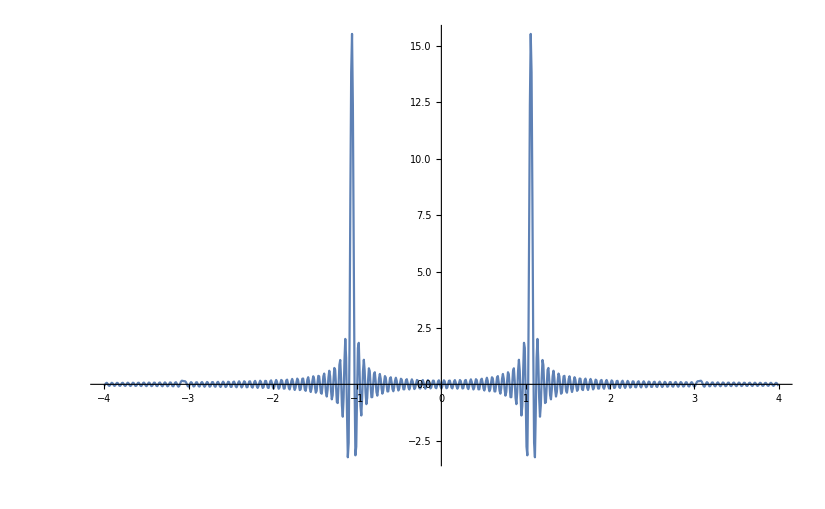

```mathematica
ListPlot[Transpose[{Range[-4,4,0.01],FTf1DTable11}],Joined->True,PlotRange->All]
```

```mathematica
Simplify[GRf1D[T,1,1]]
```

(0.-4.51388×10^-10 ⅈ) ⅇ^((0.-0.5 ⅈ) T)-(0.+4.51388×10^-10 ⅈ) ⅇ^((0.+0.5 ⅈ) T)-(0.+0.492536 ⅈ) ⅇ^((0.-1.06155 ⅈ) T)-(0.+0.492536 ⅈ) ⅇ^((0.+1.06155 ⅈ) T)-(0.+4.51388×10^-10 ⅈ) ⅇ^((0.-1.5 ⅈ) T)-(0.+4.51388×10^-10 ⅈ) ⅇ^((0.+1.5 ⅈ) T)-(0.+0.00746437 ⅈ) ⅇ^((0.-3.06155 ⅈ) T)-(0.+0.00746437 ⅈ) ⅇ^((0.+3.06155 ⅈ) T)

```mathematica
N[Eigenvalues[H]]
```

{-2.06155,2.06155,-1.,-1.,-1.,-1.,1.,1.,1.,1.,-0.5,-0.5,-0.5,0.5,0.5,0.5}